```mathematica
(*Columbic interaction of charge*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Assumptions->{Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}
```

Assumptions→{Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}

```mathematica
rhoA[r_]:=α^3 Exp[- α r]/(8 Pi)
rhoA[r]
```

(ⅇ^(-r α) α^3)/(8 π)

```mathematica
rhoB[r_]:=β^3 Exp[-β r]/(8 Pi)
rhoB[r]
```

(ⅇ^(-r β) β^3)/(8 π)

```mathematica
phiA[r_]:=4Pi((1/r )Integrate[rhoA[x] x^2,{x,0,r}]+Integrate[x rhoA[x],{x,r,Infinity},Assumptions->{Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}])
```

```mathematica
phiA[r]//Expand
```

1/r-ⅇ^(-r α)/r-1/2 ⅇ^(-r α) α

```mathematica
V1=2Pi((Integrate[r^2 rhoB[r]*Integrate[1/Sqrt[r^2+R^2-2r R x],{x,-1,1}],{r,0,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}]))//Simplify
```

(ⅇ^(-R β) (-2+2 ⅇ^(R β)-R β))/(2 R)

```mathematica
V1E=V1/.{B->A,β->α}
```

(ⅇ^(-R α) (-2+2 ⅇ^(R α)-R α))/(2 R)

```mathematica
V2=-2Pi(Integrate[r Exp[-α r]*Integrate[rhoB[Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,0,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}])
```

-(ⅇ^(-R (α+2 β)) β^3 (ⅇ^(R (α+β)) R α^2+2 ⅇ^(2 R β) β-2 ⅇ^(R (α+β)) β-ⅇ^(R (α+β)) R β^2))/(2 R (α-β)^2 (α+β)^2)

```mathematica
V2//Simplify
```

(ⅇ^(-R (α+2 β)) β^3 (-2 ⅇ^(2 R β) β+ⅇ^(R (α+β)) (2 β+R (-α^2+β^2))))/(2 R (α-β)^2 (α+β)^2)

```mathematica
V2E=Limit[V2,{β->α}]
```

{-1/8 ⅇ^(-R α) α (1+R α)}

```mathematica
V2E//Simplify
```

{-1/8 ⅇ^(-R α) α (1+R α)}

```mathematica
V3=-2Pi α/(2 ) (Integrate[r^2 rhoB[r]*Integrate[Exp[-α Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,0,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}])
```

-(ⅇ^(-R (2 α+β)) α β^3 (ⅇ^(2 R α) R α^3-4 ⅇ^(2 R α) α β+4 ⅇ^(R (α+β)) α β+ⅇ^(R (α+β)) R α^2 β-ⅇ^(2 R α) R α β^2-ⅇ^(R (α+β)) R β^3))/(2 R (α-β)^3 (α+β)^3)

```mathematica
V3//Simplify
```

-(ⅇ^(-R (2 α+β)) α β^3 (ⅇ^(R (α+β)) β (4 α+R α^2-R β^2)+ⅇ^(2 R α) α (-4 β+R (α^2-β^2))))/(2 R (α-β)^3 (α+β)^3)

```mathematica
V3E=Limit[V3,{β->α}]
```

{-1/48 ⅇ^(-R α) α (3+3 R α+R^2 α^2)}

```mathematica
V3E//Simplify
```

{-1/48 ⅇ^(-R α) α (3+3 R α+R^2 α^2)}

```mathematica
(*Full potential two diff atoms*)
V=V1+V2+V3
```

(ⅇ^(-R β) (-2+2 ⅇ^(R β)-R β))/(2 R)-(ⅇ^(-R (α+2 β)) β^3 (ⅇ^(R (α+β)) R α^2+2 ⅇ^(2 R β) β-2 ⅇ^(R (α+β)) β-ⅇ^(R (α+β)) R β^2))/(2 R (α-β)^2 (α+β)^2)-(ⅇ^(-R (2 α+β)) α β^3 (ⅇ^(2 R α) R α^3-4 ⅇ^(2 R α) α β+4 ⅇ^(R (α+β)) α β+ⅇ^(R (α+β)) R α^2 β-ⅇ^(2 R α) R α β^2-ⅇ^(R (α+β)) R β^3))/(2 R (α-β)^3 (α+β)^3)

```mathematica
V=V//Simplify
```

(ⅇ^(-R β) (-2+2 ⅇ^(R β)-R β)-(ⅇ^(-R (2 α+β)) α β^3 (ⅇ^(R (α+β)) β (4 α+R α^2-R β^2)+ⅇ^(2 R α) α (-4 β+R (α^2-β^2))))/((α-β)^3 (α+β)^3)+(ⅇ^(-R (α+2 β)) β^3 (-2 ⅇ^(2 R β) β+ⅇ^(R (α+β)) (2 β+R (-α^2+β^2))))/((α-β)^2 (α+β)^2))/(2 R)

```mathematica
(*Full potential of smame atoms*)
```

```mathematica
VE=V1E+V2E+V3E
```

{(ⅇ^(-R α) (-2+2 ⅇ^(R α)-R α))/(2 R)-1/8 ⅇ^(-R α) α (1+R α)-1/48 ⅇ^(-R α) α (3+3 R α+R^2 α^2)}

```mathematica
VE=VE//Simplify
```

{(ⅇ^(-R α) (-48+48 ⅇ^(R α)-33 R α-9 R^2 α^2-R^3 α^3))/(48 R)}

```mathematica
DerV=D[V,R]//Simplify
```

(ⅇ^(-3 R α-4 R β) (-2 ⅇ^(3 R α+4 R β) (α^2-β^2)^3+ⅇ^(2 R (α+2 β)) β^4 (6 R α^3+R^2 α^4-2 β^2-2 R α β^2+α^2 (6-R^2 β^2))+ⅇ^(3 R (α+β)) α^4 (α^2 (2+2 R β+R^2 β^2)-β^2 (6+6 R β+R^2 β^2))))/(2 R^2 (α-β)^3 (α+β)^3)

```mathematica
DerVE=D[VE,R]//Simplify
```

{(ⅇ^(-R α) (48-48 ⅇ^(R α)+48 R α+24 R^2 α^2+7 R^3 α^3+R^4 α^4))/(48 R^2)}

```mathematica
V0=Limit[V,{R->0}]
```

```mathematica
{(α β (α^2+3 α β+β^2))/(2 (α+β)^3)}
```

```mathematica
VE0=V0/.{β->α}
```

{(5 α)/16}

```mathematica
VE=(ⅇ^(-R α) (-48+48 ⅇ^(R α)-33 R α-9 R^2 α^2-R^3 α^3))/(48 R)
```

(ⅇ^(-R α) (-48+48 ⅇ^(R α)-33 R α-9 R^2 α^2-R^3 α^3))/(48 R)

```mathematica
VE
```

(ⅇ^(-R α) (-48+48 ⅇ^(R α)-33 R α-9 R^2 α^2-R^3 α^3))/(48 R)

```mathematica
α=.
```

```mathematica
Rc=.
```

```mathematica
dsf=VE-(VE/.{R->Rc})-(D[VE,R]/.{R->Rc}) (R-Rc)
```

(ⅇ^(-R α) (-48+48 ⅇ^(R α)-33 R α-9 R^2 α^2-R^3 α^3))/(48 R)-(ⅇ^(-Rc α) (-48+48 ⅇ^(Rc α)-33 Rc α-9 Rc^2 α^2-Rc^3 α^3))/(48 Rc)-(R-Rc) ((ⅇ^(-Rc α) (-33 α+48 ⅇ^(Rc α) α-18 Rc α^2-3 Rc^2 α^3))/(48 Rc)-(ⅇ^(-Rc α) (-48+48 ⅇ^(Rc α)-33 Rc α-9 Rc^2 α^2-Rc^3 α^3))/(48 Rc^2)-(ⅇ^(-Rc α) α (-48+48 ⅇ^(Rc α)-33 Rc α-9 Rc^2 α^2-Rc^3 α^3))/(48 Rc))

```mathematica
VEF=D[VE,R]//Simplify
```

(ⅇ^(-R α) (48-48 ⅇ^(R α)+48 R α+24 R^2 α^2+7 R^3 α^3+R^4 α^4))/(48 R^2)

```mathematica
dsfF=D[dsf,R]//FullSimplify
```

(ⅇ^(-(R+Rc) α) (48 ⅇ^((R+Rc) α) (R-Rc) (R+Rc)+ⅇ^(Rc α) Rc^2 (48+R α (4+R α) (12+R α (3+R α)))-ⅇ^(R α) R^2 (48+Rc α (4+Rc α) (12+Rc α (3+Rc α)))))/(48 R^2 Rc^2)

```mathematica
α=2.11725/3.64857
```

0.580296

```mathematica
Rc=25
```

25

```mathematica
apt=2
```

2

```mathematica
α=apt
```

2

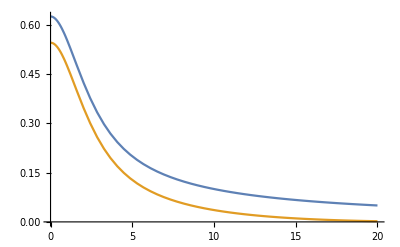

```mathematica
Plot[{VE,dsf},{R,0,20}]
```

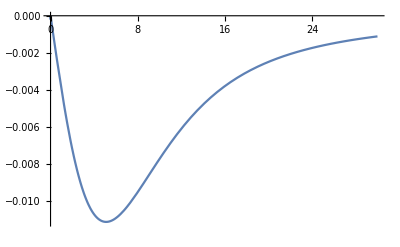

```mathematica
Plot[{VEF},{R,0,30},PlotRange->All]
```

```mathematica
VE
```

VE